```mathematica
SpinQ[S_]:=IntegerQ[2 S]&&S≥0
splus[0]={{0}}//SparseArray;
splus[S_?SpinQ]:=splus[S]=SparseArray[Band[{1,2}]->Table[Sqrt[S(S+1)-M (M+1)],{M,S-1,-S,-1}],{2 S+1,2 S+1}]
sminus[S_?SpinQ]:=Transpose[splus[S]]
sx[S_?SpinQ]:=sx[S]=(splus[S]+sminus[S])/2
sy[S_?SpinQ]:=sy[S]=(splus[S]-sminus[S])/(2 I)
sz[S_?SpinQ]:=sz[S]= SparseArray[Band[{1,1}]->Range[S,-S,-1],{2S +1,2 S+1}]
id[S_?SpinQ]:=id[S]=IdentityMatrix[2 S+1,SparseArray];
op[S_?SpinQ,L_?IntegerQ, k_?IntegerQ,a_?MatrixQ]/;
1≤k≤L&&Dimensions[a]=={2 S+1,2 S+1}:=KroneckerProduct[IdentityMatrix[(2 S+1)^(k-1),SparseArray],a,IdentityMatrix[(2 S+1)^(L-k),SparseArray]]
sx[S_?SpinQ,L_?IntegerQ,k_?IntegerQ]/;1≤k≤L:=op[S,L,k,sx[S]]
sy[S_?SpinQ,L_?IntegerQ,k_?IntegerQ]/;1≤k≤L:=op[S,L,k,sy[S]]
sz[S_?SpinQ,L_?IntegerQ,k_?IntegerQ]/;1≤k≤L:=op[S,L,k,sz[S]]
SubPlus[σ][S_?SpinQ,L_?IntegerQ,k_?IntegerQ]/;1≤k≤L:=op[S,L,k,sy[S]+I sz[S]]
Subscript[σ, x][S_?SpinQ,L_?IntegerQ,k_?IntegerQ]/;1≤k≤L:=op[S,L,k,2 sx[S]]
Subscript[σ, y][S_?SpinQ,L_?IntegerQ,k_?IntegerQ]/;1≤k≤L:=op[S,L,k,2 sy[S]]
Subscript[σ, z][S_?SpinQ,L_?IntegerQ,k_?IntegerQ]/;1≤k≤L:=op[S,L,k,2 sz[S]]
```

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 8 r = 1
 ϵ[τ] = 64 Csc[τ/4]^6 Sin[τ/2]^10

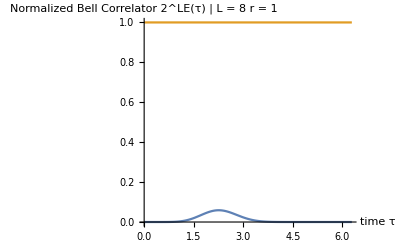

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 8 r = 2
 ϵ[τ] = 4096 Cos[τ/4]^6 (3 Cos[τ/4]+2 Cos[(3 τ)/4]+ⅈ Sin[τ/4]) Sin[τ/4]^4 (4 Cos[τ/4]+3 Cos[(3 τ)/4]+7 Cos[(5 τ)/4]+2 Cos[(7 τ)/4]-ⅈ (22 Sin[τ/4]-13 Sin[(3 τ)/4]+13 Sin[(5 τ)/4]))

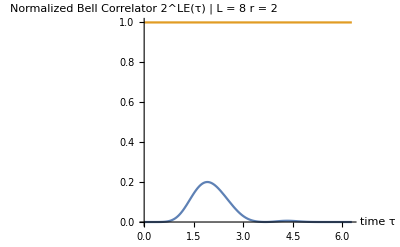

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 8 r = 3
 ϵ[τ] = 64 Sin[τ/2]^4 (6+13 Cos[τ/2]+8 Cos[τ]+5 Cos[(3 τ)/2]+3 ⅈ Sin[τ/2]+4 ⅈ Sin[τ]+3 ⅈ Sin[(3 τ)/2]) (8 Cos[τ/2]-4 Cos[τ]+15 Cos[(3 τ)/2]+4 Cos[2 τ]+9 Cos[(5 τ)/2]-ⅈ (2 Sin[τ/2]+9 Sin[(3 τ)/2]+8 Sin[2 τ]+7 Sin[(5 τ)/2]))

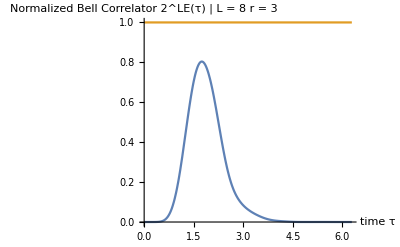

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 8 r = 4
 ϵ[τ] = 64 Sin[τ/2]^4 (12+22 Cos[τ/2]+19 Cos[τ]+12 Cos[(3 τ)/2]+5 Cos[2 τ]+6 ⅈ Sin[τ/2]+9 ⅈ Sin[τ]+8 ⅈ Sin[(3 τ)/2]+3 ⅈ Sin[2 τ]) (-18 Cos[τ/2]+19 Cos[τ]-6 Cos[(3 τ)/2]+9 Cos[2 τ]+8 Cos[(5 τ)/2]+9 Cos[3 τ]+ⅈ (-11 ⅈ+2 Sin[τ/2]-5 Sin[τ]-2 Sin[(3 τ)/2]-3 Sin[2 τ]-12 Sin[(5 τ)/2]-7 Sin[3 τ]))

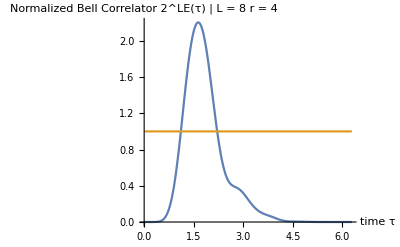

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 10 r = 1
 ϵ[τ] = 128 ⅈ Csc[τ/4]^8 Sin[τ/2]^13

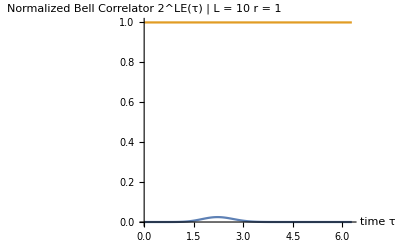

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 10 r = 2
 ϵ[τ] = 65536 ⅈ Cos[τ/4]^8 Sin[τ/4]^5 (24 Cos[τ/4]+35 Cos[(3 τ)/4]+21 Cos[(5 τ)/4]+30 Cos[(7 τ)/4]+10 Cos[(9 τ)/4]+7 Cos[(11 τ)/4]+Cos[(13 τ)/4]+ⅈ (35 Sin[τ/4]-49 Sin[(3 τ)/4]+2 Sin[(5 τ)/4]-3 (12 Sin[(7 τ)/4]+Sin[(9 τ)/4]+3 Sin[(11 τ)/4])))

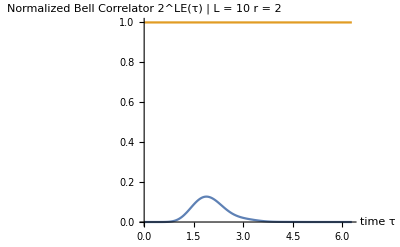

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 10 r = 3
 ϵ[τ] = 512 Sin[τ/2]^5 (7+11 Cos[τ/2]+11 Cos[τ]+6 Cos[(3 τ)/2]+3 Cos[2 τ]+3 ⅈ Sin[τ/2]+5 ⅈ Sin[τ]+4 ⅈ Sin[(3 τ)/2]+2 ⅈ Sin[2 τ]) (-5 ⅈ+17 ⅈ Cos[τ/2]-4 ⅈ Cos[τ]+17 ⅈ Cos[(3 τ)/2]+ⅈ Cos[2 τ]+23 ⅈ Cos[(5 τ)/2]+8 ⅈ Cos[3 τ]+7 ⅈ Cos[(7 τ)/2]+8 Sin[τ/2]-4 Sin[τ]+14 Sin[(3 τ)/2]+3 Sin[2 τ]+20 Sin[(5 τ)/2]+10 Sin[3 τ]+6 Sin[(7 τ)/2])

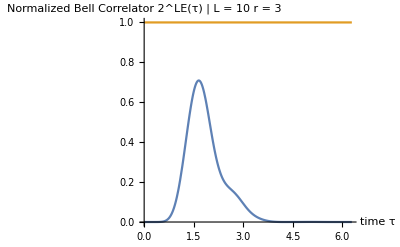

==============================================================================

Ε(τ) = 2^(-4 L)|ϵ[τ]|^2

L = 10 r = 4
 ϵ[τ] = 512 Sin[τ/2]^5 (29 Cos[τ/2]+26 Cos[τ]+18 Cos[(3 τ)/2]+11 Cos[2 τ]+4 Cos[(5 τ)/2]+Cos[3 τ]+ⅈ (-16 ⅈ+5 Sin[τ/2]+8 Sin[τ]+8 Sin[(3 τ)/2]+5 Sin[2 τ]+2 Sin[(5 τ)/2])) (-5 ⅈ+16 ⅈ Cos[τ/2]-8 ⅈ Cos[τ]+13 ⅈ Cos[(3 τ)/2]+ⅈ Cos[2 τ]+15 ⅈ Cos[(5 τ)/2]+8 ⅈ Cos[3 τ]+19 ⅈ Cos[(7 τ)/2]+4 ⅈ Cos[4 τ]+ⅈ Cos[(9 τ)/2]+2 Sin[τ/2]+2 Sin[τ]+2 Sin[(3 τ)/2]+9 Sin[2 τ]+8 Sin[(5 τ)/2]+12 Sin[3 τ]+16 Sin[(7 τ)/2]+6 Sin[4 τ])

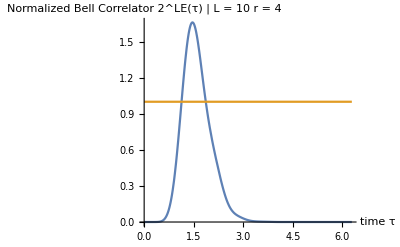

```mathematica
S=1/2;
Do[
Do[
Correlator[L,1]=SubPlus[σ][S,L,1];
Correlator[L_,i_]:=Correlator[L,i]=Correlator[L,i-1].SubPlus[σ][S,L,i];
F=2^L Correlator[L,L]//Re//IntegerPart;
H=Sum[Sum[If[j+p≤L,sz[S,L,j].sz[S,L, j+p],0],{j,1,L}] ,{p,1,r}];(*generate Hamiltonian*)  
ϵ[t_]:=Diagonal[MatrixExp[I H t]].F.Diagonal[MatrixExp[-I H t]];
Ε[t_]:=2^(-4 L) Abs[ϵ[t]]^2; 
Print["=============================================================================="];
Print["Ε(τ) = 2^(-4 L)|ϵ[τ]|^2"];
Print["L = "<>ToString[L]<>" r = "<>ToString[r]<>"\n ϵ[τ] = ",ϵ[τ]//ComplexExpand//FullSimplify//Chop];
Print[Plot[{2^L Ε[τ],1},{τ,0,2 π},AxesLabel->{"time τ","Normalized Bell Correlator  2^LΕ(τ) | L = "<>ToString[L]<>" r = "<>ToString[r] }]],
{r,1,4}],{L,8,10,2}]
```